## α

### QCD

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

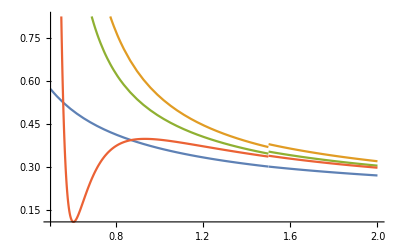

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

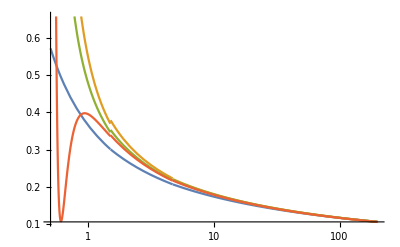

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

## μ

### QCD

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{1.715,2.08379,2.43616,2.77611,3.1062,3.42818,3.74331,4.05254}

```mathematica
Mb
```

4.7

```mathematica
Nf4α1LoopMid=Table[αs1Loop[mu]/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.285833,0.266178,0.252265,0.241701,0.233299,0.22639,0.220566,0.21556}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[mu/2]/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.396841,0.357283,0.330832,0.311546,0.296997,0.28589,0.276665,0.268835}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2mu]/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.226354,0.213849,0.204935,0.198453,0.193197,0.188807,0.185058,0.181799}

```mathematica
(* Goes into code *)
```

```mathematica
Nf4α1LoopTab=Table[α,{α,Min[Nf3α1LoopSmall],Max[Nf3α1LoopBig],(Max[Nf3α1LoopBig]-Min[Nf3α1LoopSmall])/7}]
```

{0.181799,0.21252,0.24324,0.27396,0.30468,0.335401,0.366121,0.396841}

```mathematica
Nf4δ1Loop=Nf4α1LoopTab^2
```

{0.033051,0.0451646,0.0591656,0.0750541,0.0928301,0.112493,0.134044,0.157483}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4δ1Loop)]
```

{605,443,338,266,215,178,149,127}

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{4.05254,17.822,29.8326,41.1465,52.0329,62.6156,72.9651,83.1266}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[mu]/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.21556,0.154751,0.141032,0.133637,0.128711,0.125074,0.122221,0.11989}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[mu/2]/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.268835,0.178055,0.160132,0.150667,0.144434,0.13987,0.136311,0.133418}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2mu]/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.181799,0.136841,0.126002,0.120067,0.116075,0.113109,0.11077,0.108852}

```mathematica
(* Go into code *)
```

```mathematica
Nf5α1LoopTab=Table[α,{α,Min[Nf5α1LoopSmall],Max[Nf5α1LoopBig],(Max[Nf5α1LoopBig]-Min[Nf5α1LoopSmall])/7}]
```

{0.108852,0.131707,0.154561,0.177416,0.200271,0.223126,0.24598,0.268835}

```mathematica
Nf5δ1Loop=Nf5α1LoopTab^2
```

{0.0118488,0.0173467,0.0238892,0.0314765,0.0401084,0.049785,0.0605063,0.0722722}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5δ1Loop)]
```

{1688,1153,837,635,499,402,331,277}

#### NLO

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{1.94685,2.32054,2.67764,3.02203,3.35624,3.68202,4.00065,4.31311}

```mathematica
Mb
```

4.7

```mathematica
Nf4α2LoopMid=Table[αs2Loop[mu]/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.324475,0.29642,0.277271,0.263112,0.252078,0.243152,0.235729,0.229421}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[mu/2]/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.564997,0.461228,0.404105,0.377818,0.353465,0.334731,0.319756,0.307437}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2mu]/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.238097,0.223621,0.212624,0.205469,0.199668,0.194827,0.190696,0.18711}

```mathematica
(* These 2 go into code *)
```

```mathematica
Nf4α2LoopTab=Table[α,{α,Min[Nf3α2LoopSmall],Max[Nf3α2LoopBig],(Max[Nf3α2LoopBig]-Min[Nf3α2LoopSmall])/7}]
```

{0.18711,0.241094,0.295078,0.349062,0.403045,0.457029,0.511013,0.564997}

```mathematica
Nf4α2LoopStepTab=Round[5/(.2 Nf3α2LoopTab)]
```

{134,104,85,72,62,55,49,44}

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{4.31311,18.1903,30.2405,41.5642,52.4444,63.0103,73.3356,83.4672}

```mathematica
Mt
```

173.34

```mathematica
Nf5α2LoopMid=Table[αs2Loop[mu]/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.229421,0.157949,0.14296,0.134994,0.129728,0.125862,0.122841,0.120381}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[mu/2]/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.307437,0.18467,0.164251,0.153712,0.146857,0.141879,0.138021,0.134898}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2mu]/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.18711,0.138215,0.126705,0.120457,0.116276,0.113181,0.110748,0.108756}

```mathematica
(* These 2 go into code *)
```

```mathematica
Nf5α2LoopTab=Table[α,{α,Min[Nf5α2LoopSmall],Max[Nf5α2LoopBig],(Max[Nf5α2LoopBig]-Min[Nf5α2LoopSmall])/7}]
```

{0.108756,0.137139,0.165522,0.193905,0.222288,0.250671,0.279054,0.307437}

```mathematica
Nf5α2LoopStepTab=Round[5/(.2 Nf5α2LoopTab)]
```

{230,182,151,129,112,100,90,81}

#### NNLO

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{1.88115,2.2546,2.61112,2.95474,3.28803,3.61282,3.9304,4.24177}

```mathematica
Mb
```

4.7

```mathematica
Nf4α3LoopMid=Table[αs3Loop[mu]/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.313525,0.287996,0.270383,0.257253,0.246955,0.238582,0.231589,0.225626}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[mu/2]/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.508047,0.426678,0.380431,0.34972,0.336039,0.319941,0.306917,0.296093}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2mu]/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{0.235162,0.221075,0.212612,0.205452,0.199654,0.194817,0.190693,0.187113}

```mathematica
(* These 2 go into code *)
```

```mathematica
Nf4α3LoopTab=Table[α,{α,Min[Nf3α3LoopSmall],Max[Nf3α3LoopBig],(Max[Nf3α3LoopBig]-Min[Nf3α3LoopSmall])/7}]
```

{0.187113,0.232961,0.278809,0.324656,0.370504,0.416352,0.462199,0.508047}

```mathematica
Nf4α3LoopStepTab=Round[5/(.2 Nf3α3LoopTab)]
```

{134,107,90,77,67,60,54,49}

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{4.24177,18.1659,30.2209,41.5493,52.434,63.0043,73.3338,83.4695}

```mathematica
Mt
```

173.34

```mathematica
Nf5α3LoopMid=Table[αs3Loop[mu]/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.225626,0.157737,0.142867,0.134945,0.129703,0.12585,0.122838,0.120384}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[mu/2]/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.296093,0.184024,0.163936,0.153516,0.146722,0.14178,0.137946,0.134841}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2mu]/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{0.187113,0.138172,0.126701,0.120467,0.116293,0.113203,0.110771,0.108781}

```mathematica
(* These 2 go into code *)
```

```mathematica
Nf5α3LoopTab=Table[α,{α,Min[Nf5α3LoopSmall],Max[Nf5α3LoopBig],(Max[Nf5α3LoopBig]-Min[Nf5α3LoopSmall])/7}]
```

{0.108781,0.13554,0.162299,0.189058,0.215817,0.242575,0.269334,0.296093}

```mathematica
Nf5α3LoopStepTab=Round[5/(.2 Nf5α3LoopTab)]
```

{230,184,154,132,116,103,93,84}

## M_qqbar

## M_qqq